# Notebook For : Soft Gravitons & Memory Effect For Plane Gravitational Waves

Geoff Cope
University of Utah
January 21, 2021

## Hyperlink To Original Paper

```mathematica
Hyperlink["Paper","https://arxiv.org/abs/1705.01378"]
```

[Paper](https://arxiv.org/abs/1705.01378)

## Utilities And Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 14 Kb

{Utilities`CleanSlate`,Notation`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Links To Original Papers

```mathematica
Hyperlink["Soft Gravitons & the Memory Effect for Plane Gravitational Waves",
"https://arxiv.org/abs/1705.01378"]
```

[Soft Gravitons & the Memory Effect for Plane Gravitational Waves](https://arxiv.org/abs/1705.01378)

```mathematica
Hyperlink["Gravitational Waves Penning Traps",
"https://arxiv.org/abs/1807.00765"]
```

[Gravitational Waves Penning Traps](https://arxiv.org/abs/1807.00765)

## Line Element and Metric Derivation

```mathematica
Clear[lineTometric]
lineTometric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[asubspace]
asubspace = 
Table[  If[ i ≤ j , a[i][j][u] , a[j][i][u]], {i,1,2},{j,1,2}]  ;
asubspace // MatrixForm
```

(a[1][1][u] | a[1][2][u]
a[1][2][u] | a[2][2][u])

```mathematica
Clear[metricIIpt4a]
metricIIpt4a  = 
({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
```

{{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
metricIIpt4a[[3;;4,3;;4]] = asubspace ;
metricIIpt4a // MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | a[1][1][u] | a[1][2][u]
0 | 0 | a[1][2][u] | a[2][2][u])

## Calculation of Tensors From Metric

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* we pretend i-> x , j-> y for spatial indices *) 
input[ "metricIIpt4", metricIIpt4a, "BJR","g^BJR",{u,v,x,y}, "Greek"] // Timing
```

{2.27711,Null}

```mathematica
tensorList[[1]]
TensorName[tensorList[[1]]]
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^BJR)_αβ^

BJR

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | (a(1)(1))(u) | (a(1)(2))(u)
0 | 0 | (a(1)(2))(u) | (a(2)(2))(u))

```mathematica
tensorList[[2]]
TensorName[tensorList[[2]]]
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolBJR

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
-1/2 (∂(a(1)(1))(u))/(∂u)
-1/2 (∂(a(1)(2))(u))/(∂u)) | (0
0
-1/2 (∂(a(1)(2))(u))/(∂u)
-1/2 (∂(a(2)(2))(u))/(∂u))
(0
0
((a(2)(2))(u) (∂(a(1)(1))(u))/(∂u)-(a(1)(2))(u) (∂(a(1)(2))(u))/(∂u))/(2 (a(1)(1))(u) (a(2)(2))(u)-2 ((a(1)(2))(u))^2)
((a(2)(2))(u) (∂(a(1)(2))(u))/(∂u)-(a(1)(2))(u) (∂(a(2)(2))(u))/(∂u))/(2 (a(1)(1))(u) (a(2)(2))(u)-2 ((a(1)(2))(u))^2)) | (0
0
0
0) | (((a(2)(2))(u) (∂(a(1)(1))(u))/(∂u)-(a(1)(2))(u) (∂(a(1)(2))(u))/(∂u))/(2 (a(1)(1))(u) (a(2)(2))(u)-2 ((a(1)(2))(u))^2)
0
0
0) | (((a(2)(2))(u) (∂(a(1)(2))(u))/(∂u)-(a(1)(2))(u) (∂(a(2)(2))(u))/(∂u))/(2 (a(1)(1))(u) (a(2)(2))(u)-2 ((a(1)(2))(u))^2)
0
0
0)
(0
0
((a(1)(2))(u) (∂(a(1)(1))(u))/(∂u)-(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u))/(2 ((a(1)(2))(u))^2-2 (a(1)(1))(u) (a(2)(2))(u))
((a(1)(2))(u) (∂(a(1)(2))(u))/(∂u)-(a(1)(1))(u) (∂(a(2)(2))(u))/(∂u))/(2 ((a(1)(2))(u))^2-2 (a(1)(1))(u) (a(2)(2))(u))) | (0
0
0
0) | (((a(1)(2))(u) (∂(a(1)(1))(u))/(∂u)-(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u))/(2 ((a(1)(2))(u))^2-2 (a(1)(1))(u) (a(2)(2))(u))
0
0
0) | (((a(1)(2))(u) (∂(a(1)(2))(u))/(∂u)-(a(1)(1))(u) (∂(a(2)(2))(u))/(∂u))/(2 ((a(1)(2))(u))^2-2 (a(1)(1))(u) (a(2)(2))(u))
0
0
0))

```mathematica
tensorList[[3]]
TensorName[tensorList[[3]]]
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorBJR

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (2 ((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(2)(2))(u) (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+(a(1)(1))(u) ((∂(a(1)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | (2 ((a(1)(2))(u))^2 (∂^2 (a(1)(2))(u))/(∂u^2)+(a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))-(a(1)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2)
0 | 0 | 0 | 0
-(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(2)(2))(u) (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+(a(1)(1))(u) ((∂(a(1)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | 0 | 0 | 0
-(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(2))(u))/(∂u^2)+(a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))-(a(1)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | 0 | 0 | 0) | (0 | 0 | (2 ((a(1)(2))(u))^2 (∂^2 (a(1)(2))(u))/(∂u^2)+(a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))-(a(1)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | (2 ((a(1)(2))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2))+(a(1)(1))(u) ((∂(a(2)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2)
0 | 0 | 0 | 0
-(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(2))(u))/(∂u^2)+(a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))-(a(1)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | 0 | 0 | 0
-(2 ((a(1)(2))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2))+(a(1)(1))(u) ((∂(a(2)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | -(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(2)(2))(u) (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+(a(1)(1))(u) ((∂(a(1)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | -(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(2))(u))/(∂u^2)+(a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))-(a(1)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2)
0 | 0 | 0 | 0
(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(2)(2))(u) (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+(a(1)(1))(u) ((∂(a(1)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | 0 | 0 | 0
(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(2))(u))/(∂u^2)+(a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))-(a(1)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | -(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(2))(u))/(∂u^2)+(a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))-(a(1)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | -(2 ((a(1)(2))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2))+(a(1)(1))(u) ((∂(a(2)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2)
0 | 0 | 0 | 0
(2 ((a(1)(2))(u))^2 (∂^2 (a(1)(2))(u))/(∂u^2)+(a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))-(a(1)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | 0 | 0 | 0
(2 ((a(1)(2))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (((∂(a(1)(2))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2))+(a(1)(1))(u) ((∂(a(2)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))/(4 (a(1)(1))(u) (a(2)(2))(u)-4 ((a(1)(2))(u))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]]
TensorName[tensorList[[4]]]
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorBJR

((-4 ((a(1)(2))(u))^3 (∂^2 (a(1)(2))(u))/(∂u^2)+2 ((a(1)(2))(u))^2 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 (a(2)(2))(u) (((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(1)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-2 (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (((∂(a(1)(2))(u))/(∂u))^2-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)))-4 (a(1)(1))(u) (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)/(4 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList[[5]]
TensorName[tensorList[[5]]]
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarBJR

0

```mathematica
tensorList[[6]]
TensorName[tensorList[[6]]]
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarBJR

0

```mathematica
tensorList[[7]]
TensorName[tensorList[[7]]]
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorBJR

((-4 ((a(1)(2))(u))^3 (∂^2 (a(1)(2))(u))/(∂u^2)+2 ((a(1)(2))(u))^2 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 (a(2)(2))(u) (((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(1)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-2 (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (((∂(a(1)(2))(u))/(∂u))^2-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)))-4 (a(1)(1))(u) (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)/(4 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList[[8]]
TensorName[tensorList[[8]]]
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorBJR

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (-4 ((a(1)(2))(u))^4 (∂^2 (a(1)(1))(u))/(∂u^2)+4 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))-2 ((a(1)(2))(u))^2 ((a(1)(1))(u) ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(2)(2))(u) (((∂(a(1)(1))(u))/(∂u))^2-3 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2)))+4 ((a(1)(1))(u))^2 (a(1)(2))(u) ((∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)-(a(2)(2))(u) (∂^2 (a(1)(2))(u))/(∂u^2))+(a(1)(1))(u) ((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(1)(1))(u))^3 (a(2)(2))(u) (∂^2 (a(2)(2))(u))/(∂u^2)-((a(1)(1))(u))^3 ((∂(a(2)(2))(u))/(∂u))^2)/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | (-2 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(1)(2))(u))^2 ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))-(a(1)(2))(u) (2 (a(2)(2))(u) (a(1)(1))(u) (-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 (a(1)(1))(u) (a(2)(2))(u) ((a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2)
0 | 0 | 0 | 0
(4 ((a(1)(2))(u))^4 (∂^2 (a(1)(1))(u))/(∂u^2)-4 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+2 ((a(1)(2))(u))^2 ((a(1)(1))(u) ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(2)(2))(u) (((∂(a(1)(1))(u))/(∂u))^2-3 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2)))+4 ((a(1)(1))(u))^2 (a(1)(2))(u) ((a(2)(2))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-(∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) ((a(2)(2))(u))^2 (2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2)-((∂(a(1)(1))(u))/(∂u))^2)-2 ((a(1)(1))(u))^3 (a(2)(2))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+((a(1)(1))(u))^3 ((∂(a(2)(2))(u))/(∂u))^2)/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0
(2 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (∂^2 (a(1)(1))(u))/(∂u^2))-2 ((a(1)(2))(u))^2 ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(2))(u) (2 (a(2)(2))(u) (a(1)(1))(u) (-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 (a(1)(1))(u) (a(2)(2))(u) ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))-(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0) | (0 | 0 | (-2 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(1)(2))(u))^2 ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))-(a(1)(2))(u) (2 (a(2)(2))(u) (a(1)(1))(u) (-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 (a(1)(1))(u) (a(2)(2))(u) ((a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | -(((a(2)(2))(u))^3 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(2)(2))(u))^2 (((a(1)(1))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(1)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-2 (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)))-(a(2)(2))(u) (4 ((a(1)(2))(u))^3 (∂^2 (a(1)(2))(u))/(∂u^2)-2 ((a(1)(2))(u))^2 (-3 (a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 ((a(1)(2))(u))^2 (2 ((a(1)(2))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+(a(1)(1))(u) ((∂(a(2)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2)
0 | 0 | 0 | 0
(2 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (∂^2 (a(1)(1))(u))/(∂u^2))-2 ((a(1)(2))(u))^2 ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(2))(u) (2 (a(2)(2))(u) (a(1)(1))(u) (-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 (a(1)(1))(u) (a(2)(2))(u) ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))-(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0
(((a(2)(2))(u))^3 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(2)(2))(u))^2 (((a(1)(1))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(1)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-2 (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)))-(a(2)(2))(u) (4 ((a(1)(2))(u))^3 (∂^2 (a(1)(2))(u))/(∂u^2)-2 ((a(1)(2))(u))^2 (-3 (a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 ((a(1)(2))(u))^2 (2 ((a(1)(2))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+(a(1)(1))(u) ((∂(a(2)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | (4 ((a(1)(2))(u))^4 (∂^2 (a(1)(1))(u))/(∂u^2)-4 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+2 ((a(1)(2))(u))^2 ((a(1)(1))(u) ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(2)(2))(u) (((∂(a(1)(1))(u))/(∂u))^2-3 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2)))+4 ((a(1)(1))(u))^2 (a(1)(2))(u) ((a(2)(2))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-(∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(1))(u) ((a(2)(2))(u))^2 (2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2)-((∂(a(1)(1))(u))/(∂u))^2)-2 ((a(1)(1))(u))^3 (a(2)(2))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+((a(1)(1))(u))^3 ((∂(a(2)(2))(u))/(∂u))^2)/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | (2 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (∂^2 (a(1)(1))(u))/(∂u^2))-2 ((a(1)(2))(u))^2 ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(2))(u) (2 (a(2)(2))(u) (a(1)(1))(u) (-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 (a(1)(1))(u) (a(2)(2))(u) ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))-(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2)
0 | 0 | 0 | 0
(-4 ((a(1)(2))(u))^4 (∂^2 (a(1)(1))(u))/(∂u^2)+4 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))-2 ((a(1)(2))(u))^2 ((a(1)(1))(u) ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(2)(2))(u) (((∂(a(1)(1))(u))/(∂u))^2-3 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2)))+4 ((a(1)(1))(u))^2 (a(1)(2))(u) ((∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)-(a(2)(2))(u) (∂^2 (a(1)(2))(u))/(∂u^2))+(a(1)(1))(u) ((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(1)(1))(u))^3 (a(2)(2))(u) (∂^2 (a(2)(2))(u))/(∂u^2)-((a(1)(1))(u))^3 ((∂(a(2)(2))(u))/(∂u))^2)/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0
(-2 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(1)(2))(u))^2 ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))-(a(1)(2))(u) (2 (a(2)(2))(u) (a(1)(1))(u) (-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 (a(1)(1))(u) (a(2)(2))(u) ((a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | (2 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (∂^2 (a(1)(1))(u))/(∂u^2))-2 ((a(1)(2))(u))^2 ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+(a(1)(2))(u) (2 (a(2)(2))(u) (a(1)(1))(u) (-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 (a(1)(1))(u) (a(2)(2))(u) ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))-(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | (((a(2)(2))(u))^3 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(2)(2))(u))^2 (((a(1)(1))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(1)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-2 (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)))-(a(2)(2))(u) (4 ((a(1)(2))(u))^3 (∂^2 (a(1)(2))(u))/(∂u^2)-2 ((a(1)(2))(u))^2 (-3 (a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 ((a(1)(2))(u))^2 (2 ((a(1)(2))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+(a(1)(1))(u) ((∂(a(2)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2)
0 | 0 | 0 | 0
(-2 ((a(1)(2))(u))^3 ((a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+(a(2)(2))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(1)(2))(u))^2 ((a(2)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)+(∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))-(a(1)(2))(u) (2 (a(2)(2))(u) (a(1)(1))(u) (-(a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(2)(2))(u))^2 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 (a(1)(1))(u) (a(2)(2))(u) ((a(2)(2))(u) ((∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)-2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2))+(a(1)(1))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0
-(((a(2)(2))(u))^3 (((∂(a(1)(1))(u))/(∂u))^2-2 (a(1)(1))(u) (∂^2 (a(1)(1))(u))/(∂u^2))+2 ((a(2)(2))(u))^2 (((a(1)(1))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+((a(1)(2))(u))^2 (∂^2 (a(1)(1))(u))/(∂u^2)+(a(1)(2))(u) (2 (a(1)(1))(u) (∂^2 (a(1)(2))(u))/(∂u^2)-2 (∂(a(1)(1))(u))/(∂u) (∂(a(1)(2))(u))/(∂u)))-(a(2)(2))(u) (4 ((a(1)(2))(u))^3 (∂^2 (a(1)(2))(u))/(∂u^2)-2 ((a(1)(2))(u))^2 (-3 (a(1)(1))(u) (∂^2 (a(2)(2))(u))/(∂u^2)+2 ((∂(a(1)(2))(u))/(∂u))^2+(∂(a(1)(1))(u))/(∂u) (∂(a(2)(2))(u))/(∂u))+((a(1)(1))(u))^2 ((∂(a(2)(2))(u))/(∂u))^2)+2 ((a(1)(2))(u))^2 (2 ((a(1)(2))(u))^2 (∂^2 (a(2)(2))(u))/(∂u^2)+(a(1)(1))(u) ((∂(a(2)(2))(u))/(∂u))^2-2 (a(1)(2))(u) (∂(a(1)(2))(u))/(∂u) (∂(a(2)(2))(u))/(∂u)))/(8 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]]
TensorName[tensorList[[9]]]
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorBJR

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

```mathematica
TensorValues[tensorList[[4]]][[1,1]]
```

(-4 a[1][1][u] a[1][2][u] a[1][2]'[u] a[2][2]'[u]+(a[1][1][u])^2 (a[2][2]'[u])^2+(a[2][2][u])^2 ((a[1][1]'[u])^2-2 a[1][1][u] a[1][1]''[u])-4 (a[1][2][u])^3 a[1][2]''[u]+2 (a[1][2][u])^2 ((a[1][2]'[u])^2+a[1][1]'[u] a[2][2]'[u]+a[1][1][u] a[2][2]''[u])+2 a[2][2][u] ((a[1][2][u])^2 a[1][1]''[u]+a[1][2][u] (-2 a[1][1]'[u] a[1][2]'[u]+2 a[1][1][u] a[1][2]''[u])+a[1][1][u] ((a[1][2]'[u])^2-a[1][1][u] a[2][2]''[u])))/(4 ((a[1][2][u])^2-a[1][1][u] a[2][2][u])^2)

```mathematica
Clear[eqIIpt11]
eqIIpt11 = 
b[i][j][u] == (a[i][j]'[u])/(a[i][j][u])
```

b[i][j][u]==(a[i][j]'[u])/(a[i][j][u])

```mathematica
u
```

u

```mathematica
Flatten[Solve[eqIIpt11 ,a[i][j]'[u]]]
(Flatten[Solve[eqIIpt11 ,a[i][j]'[u]]] /. {i-> k } /. {j-> l } )/. {k-> j } /. {l-> i }
```

{a[i][j]'[u]→a[i][j][u] b[i][j][u]}

{a[j][i]'[u]→a[j][i][u] b[j][i][u]}

```mathematica
?Permute
```

```mathematica
Clear[intermediate]
intermediate = 
DeleteDuplicates[Flatten[Table[
If[ i ≤ j , Flatten[Solve[eqIIpt11 ,a[i][j]'[u]]] , (Flatten[Solve[eqIIpt11 ,a[i][j]'[u]]] /. {i-> k } /. {j-> l } )/. {k-> j } /. {l-> i }  ],
{i,1,2} ,{j,1,2}] ]]
```

{a[1][1]'[u]→a[1][1][u] b[1][1][u],a[1][2]'[u]→a[1][2][u] b[1][2][u],a[1][2]''[u]→a[1][2][u] b[1][2][u],a[2][2]'[u]→a[2][2][u] b[2][2][u]}

```mathematica
Flatten[Solve[D[ eqIIpt11 ,u],a[i][j]''[u]]]
```

{a[i][j]''[u]→((a[i][j]'[u])^2+(a[i][j][u])^2 b[i][j]'[u])/(a[i][j][u])}

```mathematica
Flatten[Solve[D[ eqIIpt11 ,u],a[i][j]''[u]]] /. Flatten[Solve[eqIIpt11 ,a[i][j]'[u]]]
```

{a[i][j]''[u]→((a[i][j][u])^2 (b[i][j][u])^2+(a[i][j][u])^2 b[i][j]'[u])/(a[i][j][u])}

```mathematica
Clear[aReplace]
aReplace = {
Flatten[Solve[eqIIpt11 ,a[i][j]'[u]]] , 
(Flatten[Solve[D[ eqIIpt11 ,u],a[i][j]''[u]]] /. Flatten[Solve[eqIIpt11 ,a[i][j]'[u]]])
};
aReplace  // TableForm
```

a[i][j]'[u]→a[i][j][u] b[i][j][u]
a[i][j]''[u]→((a[i][j][u])^2 (b[i][j][u])^2+(a[i][j][u])^2 b[i][j]'[u])/(a[i][j][u])

```mathematica
Flatten[Table[aReplace[[1]] , {i,1,2},{j,1,2}]] // MatrixForm
```

(a[1][1]'[u]→a[1][1][u] b[1][1][u]
a[1][2]'[u]→a[1][2][u] b[1][2][u]
a[2][1]'[u]→a[2][1][u] b[2][1][u]
a[2][2]'[u]→a[2][2][u] b[2][2][u])

```mathematica
Flatten[Table[aReplace[[2]] , {i,1,2},{j,1,2}]] // MatrixForm
```

(a[1][1]''[u]→((a[1][1][u])^2 (b[1][1][u])^2+(a[1][1][u])^2 b[1][1]'[u])/(a[1][1][u])
a[1][2]''[u]→((a[1][2][u])^2 (b[1][2][u])^2+(a[1][2][u])^2 b[1][2]'[u])/(a[1][2][u])
a[2][1]''[u]→((a[2][1][u])^2 (b[2][1][u])^2+(a[2][1][u])^2 b[2][1]'[u])/(a[2][1][u])
a[2][2]''[u]→((a[2][2][u])^2 (b[2][2][u])^2+(a[2][2][u])^2 b[2][2]'[u])/(a[2][2][u]))

```mathematica
Clear[daReplace]
daReplace = 
Union[Flatten[Table[aReplace[[1]] , {i,1,2},{j,1,2}]] ,Flatten[Table[aReplace[[2]] , {i,1,2},{j,1,2}]] ] ;
daReplace // TableForm
```

a[1][1]'[u]→a[1][1][u] b[1][1][u]
a[1][2]'[u]→a[1][2][u] b[1][2][u]
a[2][1]'[u]→a[2][1][u] b[2][1][u]
a[2][2]'[u]→a[2][2][u] b[2][2][u]
a[1][1]''[u]→((a[1][1][u])^2 (b[1][1][u])^2+(a[1][1][u])^2 b[1][1]'[u])/(a[1][1][u])
a[1][2]''[u]→((a[1][2][u])^2 (b[1][2][u])^2+(a[1][2][u])^2 b[1][2]'[u])/(a[1][2][u])
a[2][1]''[u]→((a[2][1][u])^2 (b[2][1][u])^2+(a[2][1][u])^2 b[2][1]'[u])/(a[2][1][u])
a[2][2]''[u]→((a[2][2][u])^2 (b[2][2][u])^2+(a[2][2][u])^2 b[2][2]'[u])/(a[2][2][u])

```mathematica
TensorValues[tensorList[[4]]][[1,1]]   /. daReplace // Expand // Simplify  // pdConv
(* No idea if any of this is right *)
```

-1/(4 (((a(1)(2))(u))^2-(a(1)(1))(u) (a(2)(2))(u))^2)(2 ((a(1)(2))(u))^4 (((b(1)(2))(u))^2+2 (∂(b(1)(2))(u))/(∂u))-2 (a(1)(1))(u) (a(2)(2))(u) ((a(1)(2))(u))^2 (((b(1)(1))(u))^2+((b(2)(2))(u)-2 (b(1)(2))(u)) (b(1)(1))(u)+3 ((b(1)(2))(u))^2+((b(2)(2))(u))^2-2 (b(1)(2))(u) (b(2)(2))(u)+(∂(b(1)(1))(u))/(∂u)+2 (∂(b(1)(2))(u))/(∂u)+(∂(b(2)(2))(u))/(∂u))+((a(1)(1))(u))^2 ((a(2)(2))(u))^2 (((b(1)(1))(u))^2+((b(2)(2))(u))^2+2 ((∂(b(1)(1))(u))/(∂u)+(∂(b(2)(2))(u))/(∂u))))

```mathematica
Clear[lineElementIVpt1]
lineElementIVpt1 = 
dX1^2+ dX2^2+ 2 dU dV + 1/2 Aplus[U] ( X1^2- X2^2) dU^2
```

2 dU dV+dX1^2+dX2^2+1/2 dU^2 (X1^2-X2^2) Aplus[U]

```mathematica
Clear[metricIVpt1] (* This looks wrong see IIpt3 *) 
metricIVpt1 = 
lineTometric[ lineElementIVpt1 , {dU,dV,dX1,dX2}] ;
metricIVpt1 // MatrixForm
```

(1/2 (X1^2-X2^2) Aplus[U] | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Geodesic Equations (Need to do)

```mathematica
(* Then do geodesic equations *)
```

```mathematica
Clear[eqIVpt24]
eqIVpt24 = 
gxx[x,y] x^2+ 2 gxy[x,y] x y + gyy[x,y] y^2== 1
```

x^2 gxx[x,y]+2 x y gxy[x,y]+y^2 gyy[x,y]==1

```mathematica
Clear[eqIVpt25]
eqIVpt25 = 
gxx[x,y,t] x^2+ 2 gxy[x,y,t] x y + gyy[x,y,t] y^2== 1
```

x^2 gxx[x,y,t]+2 x y gxy[x,y,t]+y^2 gyy[x,y,t]==1

```mathematica
D[ Exp[-U^2],{U,3}]
```

12 ⅇ^(-U^2) U-8 ⅇ^(-U^2) U^3

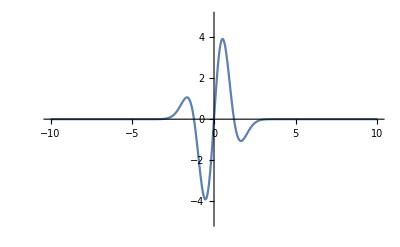

```mathematica
(* 
From page 23:
*)
Plot[
Evaluate[D[ Exp[-U^2],{U,3}] ]
, {U,-10,10}, PlotRange-> {-5,5}]
```

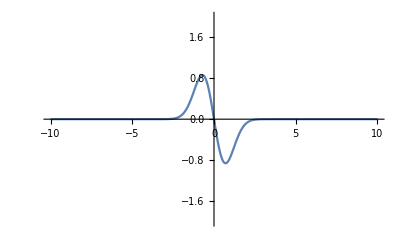

```mathematica
Plot[
Evaluate[D[ Exp[-U^2],U] ]
, {U,-10,10}, PlotRange-> {-2,2}]
```

## Links of Papers Listed

```mathematica
Hyperlink["Nicolas-Auguste Tissot: A link between cartography and quasiconformal theory",
"https://arxiv.org/abs/1612.00279"]
```

[Nicolas-Auguste Tissot: A link between cartography and quasiconformal theory](https://arxiv.org/abs/1612.00279)

```mathematica
Hyperlink["Electromagnetic waves and Stokes parameters in the wake of a gravitational wave - Hacyan",
"https://arxiv.org/abs/1206.3526"]
```

[Electromagnetic waves and Stokes parameters in the wake of a gravitational wave - Hacyan](https://arxiv.org/abs/1206.3526)

```mathematica
Hyperlink["Polarized Spinoptics and Symplectic Physics - Duval",
"https://arxiv.org/abs/1312.4486"]
```

[Polarized Spinoptics and Symplectic Physics - Duval](https://arxiv.org/abs/1312.4486)